```mathematica
pm = Import["C:\\Users\\Nikita\\Desktop\\TPM\\N_body_TPM\\Sources\\source-vs\\pm_m.txt","Table"];
```

```mathematica
PM={};
For[i=1 , i<Length[pm],i++,
AppendTo[PM, {pm[[i,1]], pm[[i,4]]}];
]
```

Part::partw: Part 4 of {15.1,0.0208926} does not exist.

Part::partw: Part 4 of {15.1,0.0208927} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
ListPlot[PM ]
```

-Graphics-

```mathematica
dir = Import["C:\\Users\\Nikita\\Desktop\\TPM\\N_body_TPM\\Sources\\source-vs\\dir_m.txt","Table"];
```

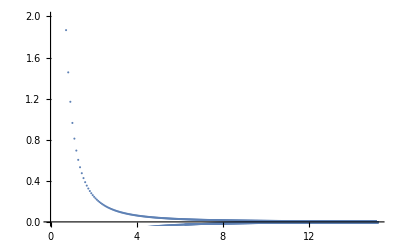

```mathematica
ListPlot[dir, PlotRange->2]
```

```mathematica
dif = {};
For[i=1 , i≤ Length[dir], i++,
AppendTo[dif, {dir[[i,1]], dir[[i, 2]]/ pm[[i,2]]}];
]
```

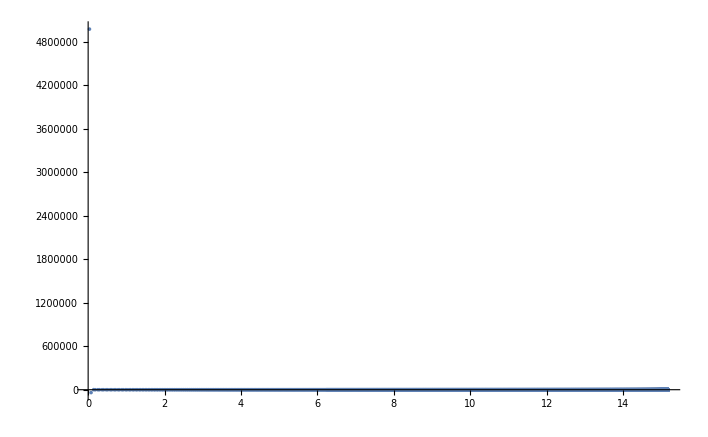

```mathematica
Show[%4, %8, PlotRange->2]
```

```mathematica
dif
```

{{15.1,0.20992},{15.1,0.20992},{15.1,0.20992},{15.0999,0.209919},{15.0999,0.209919},{15.0998,0.209919},{15.0997,0.209918},{15.0996,0.209919},{15.0995,0.209918},{15.0993,0.209917},{15.0992,0.209917},{15.099,0.209916},{15.0988,0.209915},{15.0986,0.209914},{15.0984,0.209915},3139,{6.57797,0.185958},{6.55278,0.18601},{6.5275,0.186071},{6.50213,0.186141},{6.47667,0.186222},{6.45112,0.18631},{6.42547,0.186408},{6.39973,0.186516},{6.3739,0.186633},{6.34797,0.18676},{6.32194,0.186899},{6.29583,0.187046},{6.26961,0.187205},{6.2433,0.187374}}
 |  |  |  |

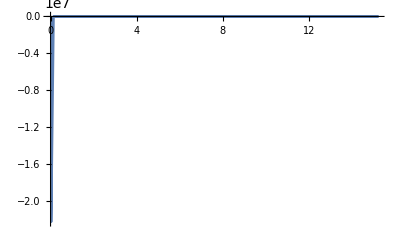

```mathematica
ListLinePlot[dif , PlotRange->All]
```

```mathematica
sh = Import["C:\\Users\\Nikita\\Desktop\\TPM\\N_body_TPM\\Sources\\source-vs\\sh_m.txt","Table"];
```

```mathematica
er={};
For[i=1 , i≤Length[sh], i++,
AppendTo[er, {sh[[i,2]], sh[[i,3]]}];
]
```

Syntax::sntxf: "AppendTo[er," cannot be followed by "[sh[[i,2]],sh[[i,3]]]]".

```mathematica
ListPlot[er]
```

-Graphics-

```mathematica
er
```

{}

```mathematica
sh
```

{{1,15.1,79.008},{2,15.1,79.008},{3,15.1,79.008},{4,15.0999,79.008},{5,15.0999,79.0081},{6,15.0998,79.0081},{7,15.0997,79.0081},{8,15.0996,79.0082},{9,15.0995,79.0082},{10,15.0993,79.0083},{11,15.0992,79.0083},{12,15.099,79.0084},{13,15.0988,79.0084},{14,15.0986,79.0085},{15,15.0984,79.0086},{16,15.0982,79.0087},{17,15.098,79.0088},{18,15.0977,79.0089},{19,15.0974,79.009},{20,15.0972,79.0091},3128,{3149,6.72726,81.4181},{3150,6.7026,81.4178},{3151,6.67785,81.4167},{3152,6.65301,81.4149},{3153,6.62808,81.4122},{3154,6.60307,81.4086},{3155,6.57797,81.4042},{3156,6.55278,81.399},{3157,6.5275,81.3928},{3158,6.50213,81.3858},{3159,6.47667,81.3779},{3160,6.45112,81.369},{3161,6.42547,81.3592},{3162,6.39973,81.3484},{3163,6.3739,81.3367},{3164,6.34797,81.3239},{3165,6.32194,81.3102},{3166,6.29583,81.2954},{3167,6.26961,81.2795},{3168,6.2433,81.2626}}
 |  |  |  |